# Integrali s parametrom

1. Narišite graf funkcije
               f(x)= ∫_0^1 sign(x-y) ⅆy.
    Najprej narišite graf funkcije
              sign(x).
    Ta enostavna funkcija je v Mathematici že vgrajena.

```mathematica
?Sign
```

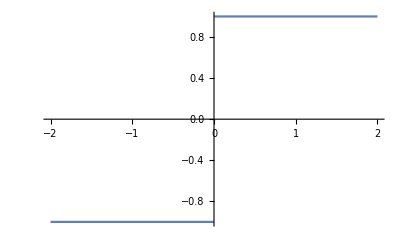

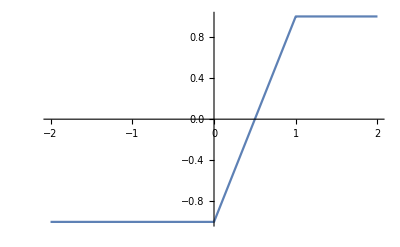

```mathematica
Clear[x]
Plot[Sign[x],{x,-2,2}]
Plot[ Integrate[Sign[x-y],{y,0,1}],{x,-2,2}]
(*na roke obravnavaš nekje je x>+ nekje -*)
```

2. Dana je funkcija
               f(x)= ∫_0^(x^2) e^(-y^2/x^2)ⅆy.
     Izračunajte približno vrednost odvoda
               f'(1).
     
     Rezultat: 1.1147

```mathematica
Clear[x,y]
f=Integrate[E^(-y^2/x^2),{y,0,x^2}]
D[f,x]/.x-> 1//N

(*Matematika integrale s parmaetrom zna risan in računat.*)
```

1/2 √π x Erf[x]

1.1147

# Dvojni integral

1. Narišite območje
               D={(x,y); (x-1)^2+y^2<1 ∧ y>(x-2)^2 }
     in izračunajte dvojni integral
               ∫∫_D x y ⅆxⅆy
	
Implicitno podane rišemo s contourPlot     
Rezultat:41/120

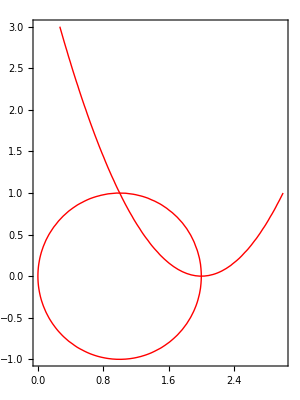

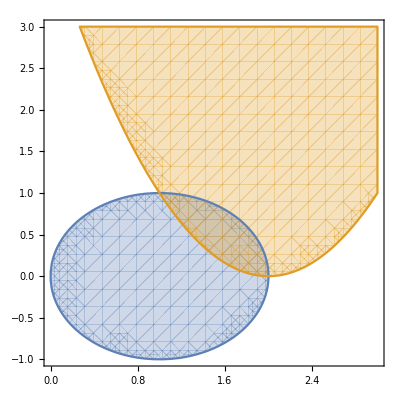

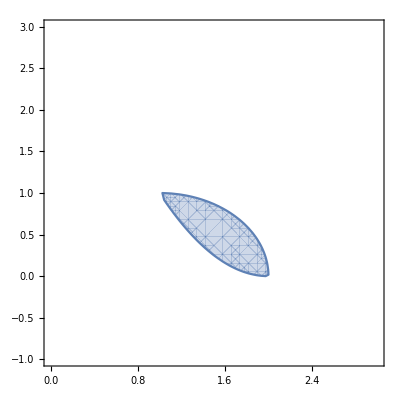

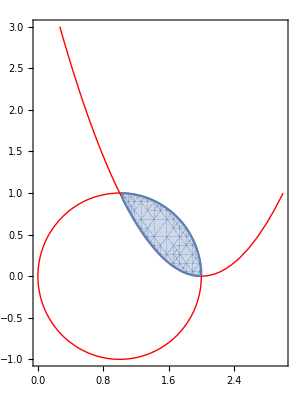

```mathematica
Clear[x,y]
slika1= ContourPlot[{(x-1)^2+y^2==1,y==(x-2)^2},{x,0,3},{y,-1,3},AspectRatio->Automatic,ContourStyle->{{Red,Thick},{Red,Thick}}]
?RegionPlot
RegionPlot[{(x-1)^2+y^2<=1,y>=(x-2)^2},{x,0,3},{y,-1,3}]
slika2=RegionPlot[{(x-1)^2+y^2<=1 && y>=(x-2)^2},{x,0,3},{y,-1,3}]
Show[slika1,slika2]
```

Ukaz Integrate:
Nedoločeni integral:	Integrate[f,x]
Določeni integral:		Integrate[f,{x,xmin,xmax}]
Dvojni integral - več seznamov:		Integrate[f,{x,xmin,xmax},{y,ymin,ymax}]   x je zunanji integral, y je notranji integral.

```mathematica
?Integrate
```

Naloga je rešena na več načinov.
Preštudirajte vsako rešitev s poudarkom na mejah integralov.

```mathematica
Solve[(x-1)^2+y^2==1,y]
Solve[(x-1)^2+y^2==1,x]
Solve[y==(x-2)^2,x]
Integrate[x y,{x,1,2},{y,(x-2)^2,Sqrt[2x-x^2]}]  (*to je zgornji primer ko projeciramo na x os. *)
Integrate[x y,{y,0,1},{x,2-Sqrt[y],1+Sqrt[1-y^2]}]

Integrate[Integrate[x y,{y,(x-2)^2,Sqrt[2x-x^2]}],{x,1,2}] (*gnezdenje integralov, je manj berljivo, hitreje se zmotimo*)

NIntegrate[x y,{x,1,2},{y,(x-2)^2,Sqrt[2x-x^2]}](*če ne gre elementarno, uporabimo numerično*)
```

{{y→-√(2 x-x^2)},{y→√(2 x-x^2)}}

{{x→1-√(1-y^2)},{x→1+√(1-y^2)}}

{{x→2-√y},{x→2+√y}}

41/120

41/120

41/120

0.341667

2. Izračunajte dvojni integral
               (∫∫)_D ⅆxⅆy/(√(4-x)),
     kjer je območje D krog v prvem kvadrantu z radijem 2, ki se dotika koordinatnih osi.
   
     Rezultat: 32/3

1/(√(4-x))

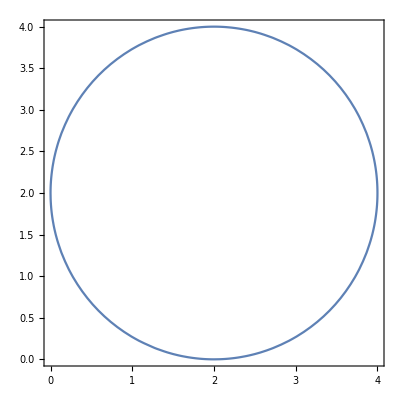

{{y→2-√(4 x-x^2)},{y→2+√(4 x-x^2)}}

32/3

```mathematica
Clear[x,y]
f=1/Sqrt[4-x]
ContourPlot[(x-2)^2 +(y-2)^2 ==4, {x,0,4},{y,0,4}]
(*na avditornih bi uorabili premaknjene polarne koordinate -DN
Tukaj pa lahko kar v kartezičnih
*)
Solve[(x-2)^2 +(y-2)^2 ==4,y]
Integrate[f,{x,0,4},{y,2-√(4 x-x^2),2+√(4 x-x^2)}]
```

3. Izračunajte dvojni integral
               ∫∫_D e^(xy^2)yⅆxⅆy,
     kjer je območje D določeno z neenačbami
               y-2x ≤ 0, 2y-x ≥0, x y ≤2.
     Območje D tudi narišite!
     tri eksplicitno podane smo naredili in Narisali.
   
     Rezultat: 9.32233

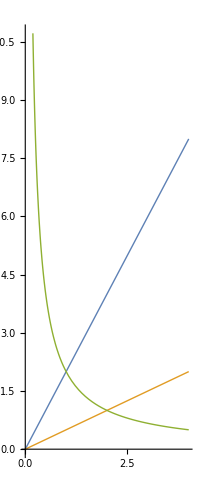

```mathematica
Clear[x,y]
s1=Plot[{2 x , x/2, 2/x}, {x, 0, 4}, AspectRatio -> Automatic, PlotStyle -> Thick]
```

Množico točk v ravnini se da osenčiti z opcijo Filling, katere uporaba je nekoliko bolj zahtevna (glejte Help). Za občutek je prikazan način osenčenja območja med dvema krivuljama.

Za risanje območij v ravnini lahko uporabljamo seveda tudi ukaz RegionPlot, katerega uporaba je v primeru spodaj.

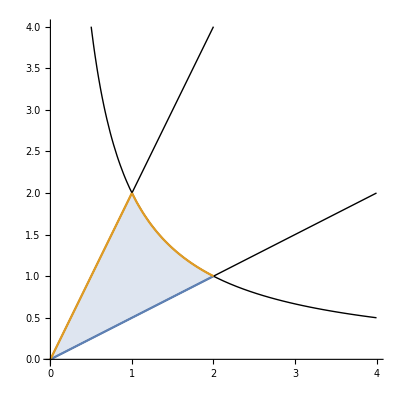

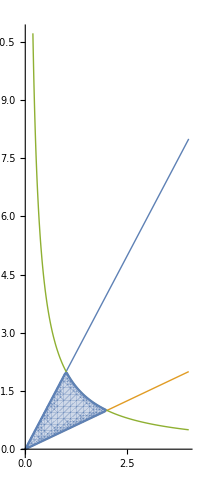

```mathematica
Show[
Plot[{2x ,x/2,2/x},{x,0,4},AspectRatio->Automatic,PlotStyle->{{Thick,Black}},PlotRange->{0,4}],
Plot[{x/2,2x},{x,0,1},Filling->{1->{2}}],
Plot[{x/2,2/x},{x,1,2},Filling->{1->{2}}]
]

RegionPlot[y-2x ≤ 0&& 2y-x ≥0&& x y ≤2,{x,0,3},{y,0,3}]
Show[s1,%] (* % je zadnji izračunan rezultat*)
```

```mathematica
f=E^(x y^2)y

Solve[{y==2x,y==2/x},{x,y}]
Solve[{y==x/2,y==2/x},{x,y}]
NIntegrate[f,{x,0,1},{y,x/2,2x}]+NIntegrate[f,{x,1,2},{y,x/2,2/x}]
(*DN zapiši še v drugem vrstnem redu*)
```

ⅇ^(x y^2) y

{{x→-1,y→-2},{x→1,y→2}}

{{x→-2,y→-1},{x→2,y→1}}

9.32233

4. Izračunajte ploščino lika, ki ga dobite s presekom
               r ≤ 4 (1 + cosφ),
               x ≥ 3.     ContourPlot bi bla tud opcija. 
               
               X= rCos(fi)
               3= rCos(fi) -> r=

     Rezultat: 9 √3+8 π

Krivuljo, ki je dana v polarnih kordinatah, lahko narišemo z ukazom PolarPlot.

{{r→3 Sec[fi]}}

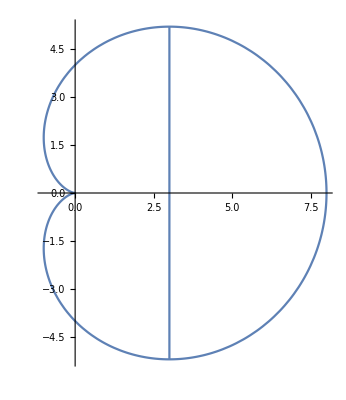

{{φ→ConditionalExpression[-π/3+2 π C[1],C[1]∈ℤ]},{φ→ConditionalExpression[π/3+2 π C[1],C[1]∈ℤ]},{φ→ConditionalExpression[-ArcCos[-3/2]+2 π C[1],C[1]∈ℤ]},{φ→ConditionalExpression[ArcCos[-3/2]+2 π C[1],C[1]∈ℤ]}}

r

9 √3+8 π

```mathematica
Solve[r Cos[fi]==3,r]
Krivulja1 = PolarPlot[4 (1 + Cos[φ]), {φ,0, 2 π}];
Krivulja2 = PolarPlot[3 / Cos[φ], {φ,-π/3,π/3}];
Show[Krivulja1, Krivulja2]
Solve[4 (1 + Cos[φ])==3 / Cos[φ] ,φ]
J=r
Integrate[1*J,{φ, -Pi/3,Pi/3}, {r,3 / Cos[φ],4 (1 + Cos[φ])}]
```

5. Izračunajte izlimitiran dvojni integral
               (∫∫)_D ⅇ^(-(x+y)^2)ⅆxⅆy,
     kjer je območje D določeno z
               x ≥ 0, y ≥ 0,
     tako da uvedete novi spremenljivki
               x = r cos^2t
               y = r sin^2t

     Rezultat: 1/2

```mathematica
x=r Cos[t]^2
y=r Sin[t]^2
f=E^(-(x+y)^2)
J= Det[{{D[x,r],D[x,t]},{D[y,r],D[y,t]}}]//Simplify
Integrate[f*J,{t, 0, Pi/2},{r,0,Infinity}]
```

r Cos[t]^2

r Sin[t]^2

ⅇ^(-(r Cos[t]^2+r Sin[t]^2)^2)

r Sin[2 t]

1/2

# Trojni integral

```mathematica
Slikab = ParametricPlot3D[{2 Cos[u] + 2, 2 Sin[u], v}, {u, 0, 2π}, {v, 0, 5}]
Slikac = Plot3D[y, {x,-5,5}, {y, -5, 5}]
Show[Slikab, Slikac]
```

-Graphics3D-

-Graphics3D-

1. Izračunajte prostornino telesa, omejenega s ploskvami:
               z = √(x^2+y^2),stožec
x^2+y^2 = 4 x,premaknjen valj
z = 0.ravnina
     Poglejte si rešitev tako z dvojnim kot s trojnim integralom.

     Rezultat: 256/9

Namig: Za risanje danega valja lahko uporabimo parametrizacijo
x = 2 Cos[u] + 2
y = 2 Sin[u]
z = v

```mathematica
Clear[r,z]
Slika1=ParametricPlot3D[{r Cos[φ],r Sin[φ],r},{φ,0,2π},{r,0,5}]
Slika2 = ParametricPlot3D[{2 Cos[u] + 2, 2 Sin[u], v}, {u, 0, 2π}, {v, 0, 7}]
Slika3 = Plot3D[0, {x,-5,5}, {y, -5, 5}]
Show[Slika1, Slika2, Slika3,ViewPoint->{2.720, -2.012, -0.026}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

```mathematica
(*nepremeknjene cilindrične*)
J=r
2* Integrate[1*J,{fi, 0,Pi/2},{r,0,4 Cos[fi]},{z,0,r}]
2* Integrate[(r-0)1*J,{fi, 0,Pi/2},{r,0,4 Cos[fi]}] (*z dvojnim*)
```

r

256/9

256/9

2. Določite težišče 1/8 krogle
               x^2+ y^2 + z^2 ≤ 1,
     ki leži v prvem oktantu, če je gostota enaka
               ρ = 1/(√(1-(x^2+y^2+z^2))).
     
     Rezultat: {4/(3π),4/(3π),4/(3π)}

Formula za posamezno koordinato težišča se glasi
x_T=((∫∫∫)_V x ρⅆxⅆyⅆz)/((∫∫∫)_V ρⅆxⅆyⅆz),     y_T=((∫∫∫)_V y ρⅆxⅆyⅆz)/((∫∫∫)_V ρⅆxⅆyⅆz),     z_T=((∫∫∫)_V z ρⅆxⅆyⅆz)/((∫∫∫)_V ρⅆxⅆyⅆz)

Namig: Uvedite sferične koordinate! !

```mathematica
x=r Cos[fi]Sin[th]
y=r Sin[fi]Sin[th]
z=r Cos[th]
J=r^2 Sin[th]

ro=1/Sqrt[1-(x^2+y^2+z^2)]
m= Integrate[ro*J,{fi,0,Pi/2}, {th,0,Pi/2},{r,0,1}]
xt =1/m Integrate[x ro*J,{fi,0,Pi/2}, {th,0,Pi/2},{r,0,1}](*Zaradi Simetrije telesa IN gostote, in je gostota simetrična so vse enake, ampak vseeno:*)
yt =1/m Integrate[y ro*J,{fi,0,Pi/2}, {th,0,Pi/2},{r,0,1}]
zt =1/m Integrate[z ro*J,{fi,0,Pi/2}, {th,0,Pi/2},{r,0,1}]
```

r Cos[fi] Sin[th]

r Sin[fi] Sin[th]

r Cos[th]

r^2 Sin[th]

1/(√(1-r^2 Cos[th]^2-r^2 Cos[fi]^2 Sin[th]^2-r^2 Sin[fi]^2 Sin[th]^2))

π^2/8

4/(3 π)

4/(3 π)

4/(3 π)

# Dodatne naloge

1. Izračunajte trojni integral
               (∫∫∫)_V 1/(x + y + z + 1)^3 ⅆxⅆyⅆz,
     kjer je območje V določeno z
               x > 0,  y > 0,  z > 0,  x + y + z < 1.
   
     Rezultat: -5/16+Log[2]/2

```mathematica
Clear[x,y,z]
S1=ParametricPlot3D[{0, u, v}, {u, 0, 1.5}, {v, 0, 1.5}];
S2=ParametricPlot3D[{u, 0, v}, {u, 0, 1.5}, {v, 0, 1.5}];
S3=ParametricPlot3D[{u, v, 0}, {u, 0, 1.5}, {v, 0, 1.5}];
S4=Plot3D[1-x-y, {x, 0, 1}, {y, 0, 1}];
Show[S1, S2, S3, S4, ViewPoint->{2.326, 1.637, 1.833}]

f=1/(x+y+z+1)^3
Integrate[f, {x,0,1},{y,0,-x+1},{z,0,1-x-y}]
```

-Graphics3D-

1/(1+x+y+z)^3

-5/16+Log[2]/2

2. Izračunajte prostornino telesa, omejenega z danima ploskvama:
               z = 6 - x^2 - y^2,  z = √(x^2+ y^2).

     Navodilo: vpeljite cilindrične koordinate!
   
     Rezultat:(32 π)/3

```mathematica
S1=ParametricPlot3D[{r Cos[fi],r Sin[fi],6-r^2},{fi,0,2Pi},{r,0,2}];
S2= ParametricPlot3D[{r Cos[fi],r Sin[fi],r},{fi,0,2Pi},{r,0,2}];
Show[S1,S2,PlotRange->All]
x= r*Cos[fi]
y= r* Sin[fi] 
z= z
J= r
Solve[6-r^2==r] 
Integrate[1*J, {fi,0,2Pi},{r,0,2},{z,r,6-r^2}]
```

-Graphics3D-

r Cos[fi]

r Sin[fi]

z

r

{{r→-3},{r→2}}

(32 π)/3

3. Izračunajte izlimitiran trojni integral
               (∫∫∫)_V 1/((x^2 + y^2 + z^2)^3)ⅆxⅆyⅆz,
     kjer je območje V določeno z
               x ≥ 0,  y ≥ 0,  z ≥ 0,  x^2 + y^2 + z^2 ≥ 1

     Navodilo: vpeljite sferične koordinate!

     Rezultat: π/6

```mathematica
S1=ParametricPlot3D[{Cos[φ] Cos[θ], Sin[φ] Cos[θ], Sin[θ]}, {φ, 0, 2Pi}, {θ, -Pi/2, Pi/2}];
S2=ParametricPlot3D[{0, u, v}, {u, 0, 2}, {v, 0, 2}];
S3=ParametricPlot3D[{u, 0, v}, {u, 0, 2}, {v, 0, 2}];
S4=ParametricPlot3D[{u, v, 0}, {u, 0, 2}, {v, 0, 2}];
Show[S1, S2, S3, S4, ViewPoint->{2.326, 1.637, 1.833}]
```

-Graphics3D-

```mathematica
Clear[x,y,z,fi,th]
x=r Cos[fi]Sin[th]
y=r Sin[fi]Sin[th]
z=r Cos[th]
J=r^2 Sin[th]

F= 1/(x^2+y^2+z^2)^3
Integrate[ F*J,{th,0,Pi/2},{fi,0,Pi/2},{r,1,Infinity}]
```

r Cos[fi] Sin[th]

r Sin[fi] Sin[th]

r Cos[th]

r^2 Sin[th]

1/((r^2 Cos[th]^2+r^2 Cos[fi]^2 Sin[th]^2+r^2 Sin[fi]^2 Sin[th]^2)^3)

π/6